```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics",All],FontFamily->"CMU Serif"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
SetDirectory[NotebookDirectory[]];
<<CustomTicks`
ww0m1 = Import["ww0m1_partonic.dat","List"];
ww01 = Import["ww01_partonic.dat","List"];
ww10 = Import["ww10_partonic.dat","List"];
wwm10 = Import["wwm10_partonic.dat","List"];
ww00 = Import["ww00_partonic.dat","List"];
dytw00 = Import["ww00_partonic_dyt015.dat","List"];
dytw11 = Import["ww11_partonic_dyt015.dat","List"];
dytwm1m1 = Import["wwm1m1_partonic_dyt015.dat","List"];
mdytw00 = Import["ww00_partonic_dytm015.dat","List"];
mdytw11 = Import["ww11_partonic_dytm015.dat","List"];
mdytwm1m1 = Import["wwm1m1_partonic_dytm015.dat","List"];
```

```mathematica
ww11 = Import["ww11_partonic.dat","List"];
wwm1m1 = Import["wwm1m1_partonic.dat","List"];
ww1m1 = Import["ww1m1_partonic.dat","List"];
wwm11 = Import["wwm11_partonic.dat","List"];
sqrtsList=Table[350+25*i,{i,0,400}];
```

```mathematica
zz0m1 = Import["zz0m1_partonic.dat","List"];
zz01 = Import["zz01_partonic.dat","List"];
zz10 = Import["zz10_partonic.dat","List"];
zzm10 = Import["zzm10_partonic.dat","List"];
zz00 = Import["zz00_partonic.dat","List"];
```

```mathematica
dytz00 = Import["zz00_partonic_dyt015.dat","List"];
dytz11 = Import["zz11_partonic_dyt015.dat","List"];
dytzm1m1 = Import["zzm1m1_partonic_dyt015.dat","List"];
mdytz00 = Import["zz00_partonic_dytm015.dat","List"];
mdytz11 = Import["zz11_partonic_dytm015.dat","List"];
mdytzm1m1 = Import["zzm1m1_partonic_dytm015.dat","List"];
```

```mathematica
zz11 = Import["zz11_partonic.dat","List"];
zzm1m1 = Import["zzm1m1_partonic.dat","List"];
zz1m1 = Import["zz1m1_partonic.dat","List"];
zzm11 = Import["zzm11_partonic.dat","List"];
```

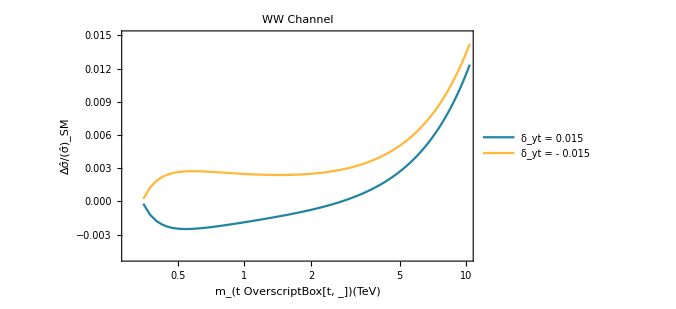

```mathematica
factor=0.3894*10^12;
nonlinearlineplot=ListPlot[{Transpose[{sqrtsList/10^3,(dytw00+dytw11+dytwm1m1-ww00-ww11-wwm1m1)/(ww00+ww01+ww0m1+ww10+wwm10+ww11+wwm1m1+ww1m1+wwm11)}],Transpose[{sqrtsList/10^3,(mdytw00+mdytw11+mdytwm1m1-ww00-ww11-wwm1m1)/(ww00+ww01+ww0m1+ww10+wwm10+ww11+wwm1m1+ww1m1+wwm11)}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][6],ColorData[colorselecitonumber][2],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9]},Frame->True,BaseStyle->{FontFamily->"Times"},ScalingFunctions->{"Log",None},FrameLabel->{Style["m_(t OverscriptBox[t, _])(TeV)",Black,17,FontFamily->"Times"],Style["Δσ̂/(σ̂)_SM",Black,17,FontFamily->"Times"]},
PlotLabel->Style["WW Channel",Black,17],
PlotLegends->Placed[{Style[" δ_yt =    0.015 ",Black,15,FontFamily->"Times"],Style[" δ_yt = - 0.015",Black,15,FontFamily->"Times"]},{0.22,0.8}],
PlotRange->{{.300,10},{-0.005,0.015}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicksStyle->Directive[Black,15],ImageSize->500]
(*customticks package*)
```

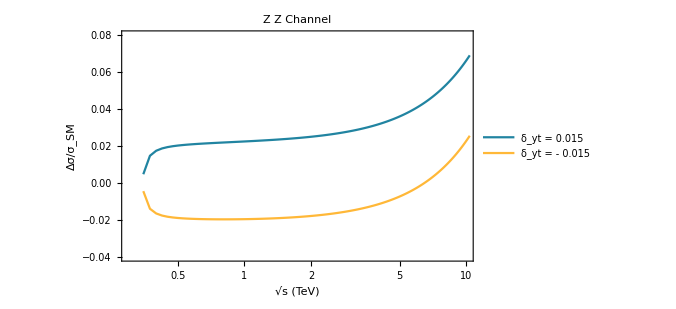

```mathematica
nonlinearlineplot1=ListPlot[{Transpose[{sqrtsList/10^3,(dytz00+dytz11+dytzm1m1-zz00-zz11-zzm1m1)/(zz00+zz01+zz0m1+zz10+zzm10+zz11+zzm1m1+zz1m1+zzm11)}],Transpose[{sqrtsList/10^3,(mdytz00+mdytz11+mdytzm1m1-zz00-zz11-zzm1m1)/(zz00+zz01+zz0m1+zz10+zzm10+zz11+zzm1m1+zz1m1+zzm11)}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][6],ColorData[colorselecitonumber][2],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9]},Frame->True,BaseStyle->{FontFamily->"Times"},ScalingFunctions->{"Log",None},FrameLabel->{Style["\!\(\*SqrtBox[\(s\)]\) (TeV)",Black,17,FontFamily->"Times"],Style["Δσ/σ_SM",Black,17,FontFamily->"Times"]},
PlotLabel->Style["Z Z Channel",Black,17],
PlotLegends->Placed[{Style[" δ_yt =    0.015 ",Black,15,FontFamily->"Times"],Style[" δ_yt = - 0.015",Black,15,FontFamily->"Times"]},{0.22,0.8}],
PlotRange->{{.300,10},{-0.04,0.08}},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicksStyle->Directive[Black,15],ImageSize->500]
```

```mathematica
ticks0=LogTicks[10,-2,6,TickLabelStep->2];
ticks1=ticks0;
Do[ticks1[[i,1]]=10^(ticks0[[i,1]]),{i,1,Length[ticks0]}]
ticks1;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ishmammahbub/Desktop/Research/Partonic Distribution/WWtt/Plot Partonic Distribution/untitled folder

```mathematica
(*Export["WW_partonic_dyt.pdf",lineplot]
Export["ZZ_partonic_dyt.pdf",lineplot1]
```